```mathematica
dropPortFunction[α_,t_,θ_]=(α^2 (1-(α t)^2)(1-t^2))/(1+( t α)^4 -2(t α)^2 Cos[θ]);
```

```mathematica
dropPortFunction
```

```mathematica
dir="Documents//thesis//";
```

```mathematica
dropPortData=Table[{λ,10Log[10,dropPortFunction[0.999,0.95,2π λ/FSR]]/.FSR->1},{λ,1497.5,1502.5,0.01}];
```

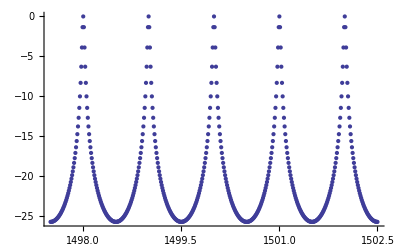

```mathematica
ListPlot[dropPortData]
```

```mathematica
Export[dir<>"test.dat",dropPortData];
```